```mathematica
SetDirectory[NotebookDirectory[]];
xy0=Import["xy0.txt","Table"];
xy1=Import["xy1.txt","Table"];
xy2=Import["xy2.txt","Table"];
```

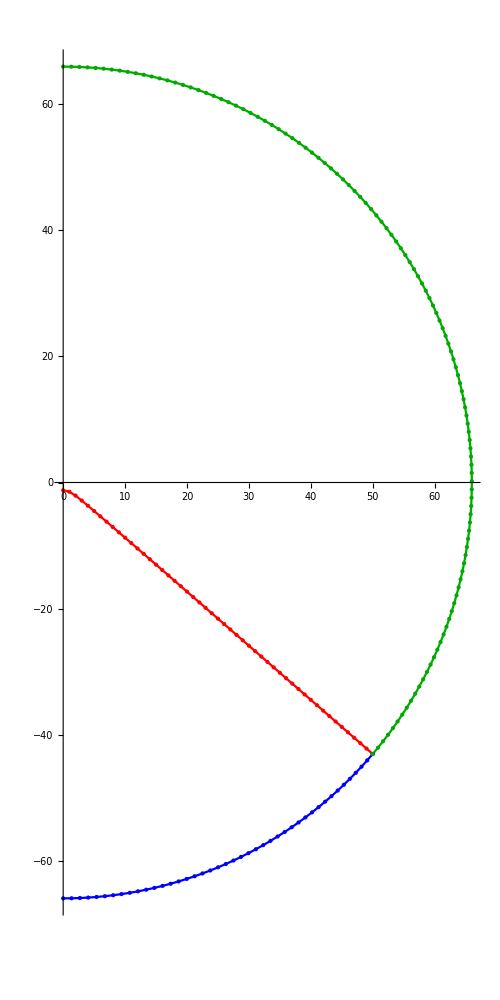

```mathematica
ListPlot[{xy0,xy1,xy2},PlotStyle->{Red,Blue,Darker@Green},
AspectRatio->Automatic,Joined->True,Epilog->{Red,Point@xy0,Blue,Point[xy1],Darker@Green,Point[xy2]}]//Rotate[#,π/2]&
```